```mathematica
$Assumptions=k∈Reals;
m=1;
ω[q_]:=Sqrt[q^2+m^2]
```

```mathematica
Integrate[1/(ω[q1]ω[q2]ω[q1+q2+k]) 1/(ω[q1]+ω[q2]+ω[q1+q2+k]+ω[k]),{q1,-Infinity,Infinity},{q2,-Infinity,Infinity}]
```

$Aborted

```mathematica
f2[k_]:=1/ω[k]^2NIntegrate[1/(ω[q1]ω[q2]ω[q1+q2+k]) 1/(ω[q1]+ω[q2]+ω[q1+q2+k]+ω[k]),{q1,-Infinity,Infinity},{q2,-Infinity,Infinity}]
```

```mathematica
data1=Table[{k,f2[k]},{k,0,6,.05}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

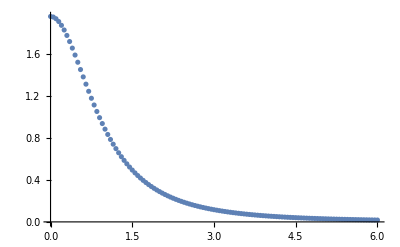

```mathematica
ListPlot[data1]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/lorenzo/Phi4

```mathematica
v =Import["data2p.csv","Data"];
data2=ArrayReshape[v,{Length[v⟦1⟧]/2,2}];
data2⟦All,2⟧=data2⟦All,2⟧*data1⟦1,2⟧/data2⟦1,2⟧;
```

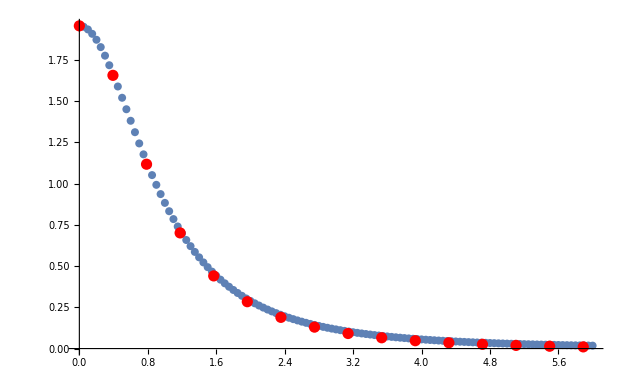

```mathematica
Show[ListPlot[data1],ListPlot[data2,PlotStyle->{Red} ]]
```